```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/blogit" ]
```

/Users/peeter/project/figures/blogit

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

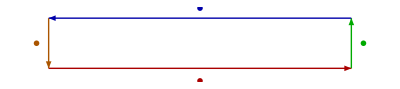

```mathematica
ClearAll[ RectangularContourFig1, a, b ]
a = 3;
b = 1;
RectangularContourFig1 = Graphics[{
Thick,
Black,
  Arrowheads[0.04],

Red//Darker,
  Arrow[{{-a,-b},{a,-b}}],
Text[MaTeX["\\color{RedDarker}I"], {0, -1.25 b}],

Green//Darker,
  Arrow[{{a,-b},{a,0}}],
Text[MaTeX["\\color{GreenDarker}K"], {1.08 a, -b/2}],

Blue//Darker,
  Arrow[{{a,0},{-a,0}}],
Text[MaTeX["\\color{BlueDarker}J"], {0, 0.2 }],

Orange//Darker,
  Arrow[{{-a,0},{-a,-b}}],
Text[MaTeX["\\color{OrangeDarker}L"], {-1.08 a, -b/2}],

}]
```

```mathematica
peeters`exportForLatex["RectangularContourFig1", RectangularContourFig1]
```

{RectangularContourFig1.eps,RectangularContourFig1pn.png}

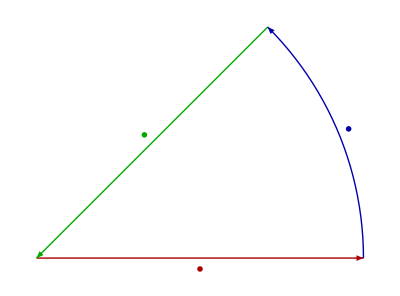

```mathematica
ClearAll[ PieContourFig2, r, o, e1, e2, z, tHat, rHat, startPoint, arc, rr, midPoint]
r = 3;
o = {0,0};
e1 = {1,0};
e2 = {0,1};
rr[t_] := {Cos[t], Sin[t]};
rHat = rr[Pi/4];
tHat = (1/Sqrt[2])(e2 - e1);
z = r rHat;

startPoint=r e1;
midPoint = r rr[Pi/8];
arc=Table[r rr[t],{t,0, Pi/4,Pi/100}];

PieContourFig2 = Graphics[{
Thick,
Black,
  Arrowheads[0.04],

Red//Darker,
  Arrow[{o, startPoint}],
Text[MaTeX["\\color{RedDarker}I"],startPoint/2 - 0.1 e2],

Green//Darker,
  Arrow[{z, o}],
Text[MaTeX["\\color{GreenDarker}K"], z/2 + 0.1 tHat ],

Blue//Darker,
Arrow[arc],
Text[MaTeX["\\color{BlueDarker}J"], 0.1rr[Pi/8] + midPoint]

}]
```